```mathematica
Clear["Global'*"];
Remove["Global`*"];
Gauss[x_,y_, x0_, y0_] := I0*1/(σx*σy*Pi*2)* Exp[-((x-x0)^2/(2σx^2)+(y-y0)^2/(2σy^2))];
xcenter[t_]:= TriangleWave[{-Vx/2,Vx/2},fx*t];
ycenter[t_]:= TriangleWave[{-Vy/2,Vy/2},fy*t];
vars = { I0-> 1,
	σx -> .3,
	σy -> .3,
	Vx -> 2,
	fx -> 25,
	Vy->2,
	fy ->307};
TriangleApprox[A_, t_]=A*Sum[8/Pi^2(-1)^k(Sin[2Pi(2k+1)t])/(2k+1)^2,{k,0,3}];
xcenter1[t_]= TriangleApprox[Vx/2.,fx*t]/.vars//FullSimplify
ycenter1[t_]= TriangleApprox[Vy/2.,fy*t]/.vars//FullSimplify;
```

0.810569 Sin[50 π t]-0.0900633 Sin[150 π t]+0.0324228 Sin[250 π t]-0.0165422 Sin[350 π t]

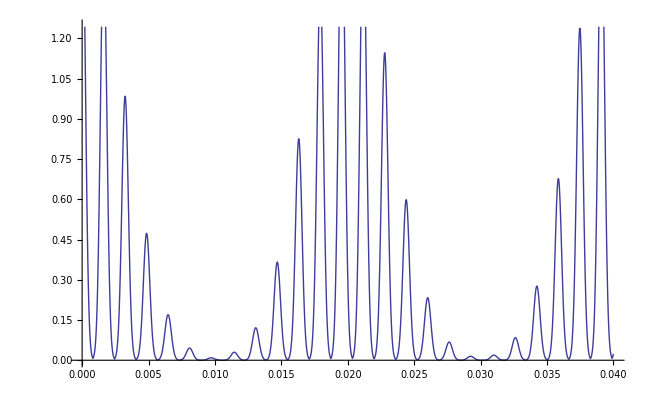

```mathematica
Plot[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,0,.04}]
```

```mathematica
F[{x_,y_}]:={x,y,Gauss[0,0,x,y]/.vars}
F1[{x_,y_,t_}] :={t,Gauss[x,y,xcenter1[t],ycenter1[t]]/.vars}
F2[{x_,y_,t1_}]:={t1,NIntegrate[Gauss[0,0,xcenter1[t],ycenter1[t]]/t/.vars,{t,0.00001,t1}]}
F3[{x_,y_,t1_}]:={t1,Integrate[Gauss[0,0,xcenter1[t],ycenter1[t]]/t/.vars,{t,0.00001,t1}]}
```

```mathematica
Plot[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,0.05,100/(2*307)}]
Integrate[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,0,20/(2*307)}]//AbsoluteTiming
j=4;
```

```mathematica
f4[t1_]:={t1,1/t1 *Sum[Integrate[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,(i-4)/(2*307),i/(2*307)}],{i,4,t1*2*307,4}]}
points1 = Flatten[Table[{t},{t,2/307,.25,4/(2*307)}],1];
```

```mathematica
bob=ParallelMap[f4,points1];
```

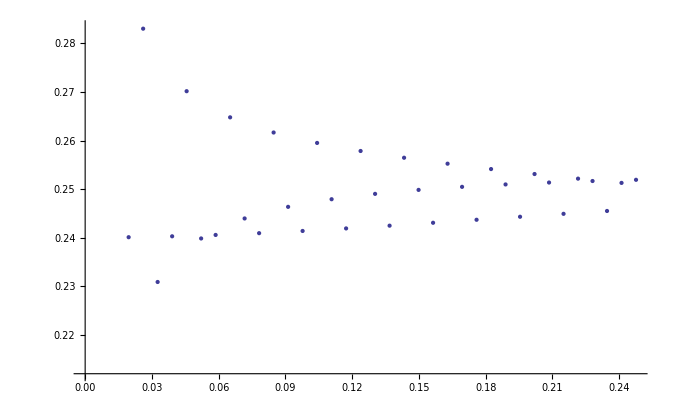

```mathematica
bob1=ListPlot[bob]
```

```mathematica
Show[Plot[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,0,120/(2*307)}],bob1]
```

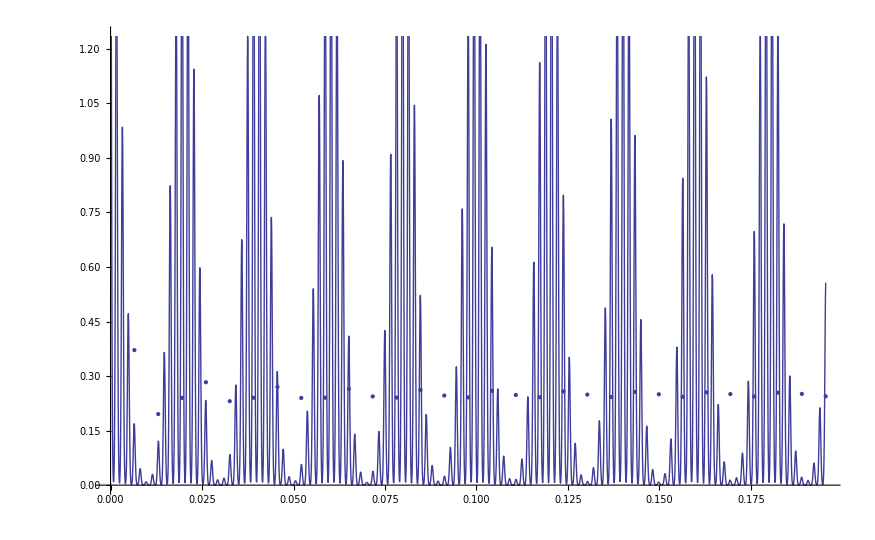

```mathematica
ListPlot[ParallelMap[f4,points1]]
```

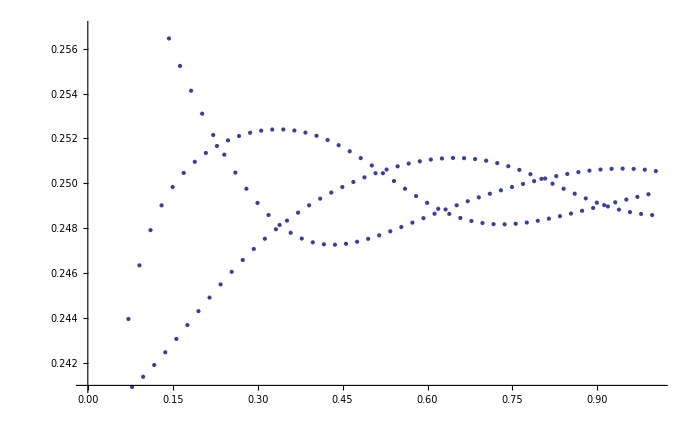
```mathematica
pl-Graphics-
```

```mathematica
For[j1=1,j1<23,j1++,Print[{f4[list[[j1]]],list[[j1]]}]]
```

{{401.7211259,0.0477474},1}

{{299.593782,0.0477474},2}

{{252.289853,0.0477474},3}

{{229.24472,0.0477474},4}

{{228.511984,0.0477474},5}

{{212.462071,0.0477474},6}

{{203.653822,0.0477474},8}

{{202.739983,0.0474212},9}

{{203.648378,0.0477474},10}

{{195.213039,0.0477474},12}

{{193.892272,0.0477474},15}

{{179.720652,0.0428639},18}

{{190.156963,0.0477474},20}

{{188.012294,0.0477474},24}

{{190.823406,0.0477474},30}

{{179.990589,0.0428639},36}

{{187.937579,0.0477474},40}

{{190.620441,0.0477474},60}

{{171.804164,0.028367},72}

{{174.497422,0.0373632},90}

{{185.389299,0.0477474},120}

{{0.,0},180}

```mathematica
Sum[Integrate[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,(i-120)/(2*307),i/(2*307)}],{i,120,360,120}]//AbsoluteTiming
f4[120]
```

{282.374421,0.147156}

{206.253461,0.0477474}

```mathematica
list={1,2,3,4,5,6,8,9,10,12,15,18,20,24,30,36,40,60,72,90,120,180};
```

```mathematica
points = Flatten[Table[{i,j},{i,-1,1,.1},{j,-1,1,.1}],1];
points2 = Flatten[Table[{0,0,t},{t,.01,.025,.0001}],0];
```

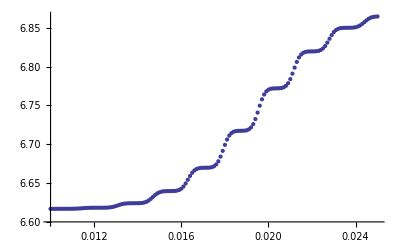

```mathematica
ListPlot[Map[F2,points2]]
```

```mathematica
ListPlot[ParallelMap[F2,points2]]
```

-Graphics-

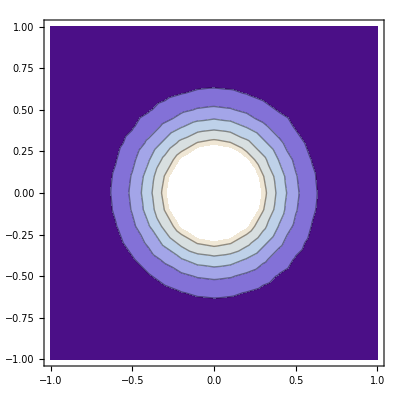
{3.9907678,-Graphics-}

{5.7820959,-Graphics-}

```mathematica
ListContourPlot[Map[F,points]]//AbsoluteTiming
ListContourPlot[ParallelMap[F,points]]//AbsoluteTiming
```

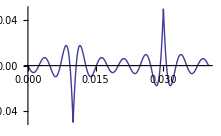

```mathematica
Plot[{xcenter1[t]-TriangleWave[{-1,1},25*t]/.vars//FullSimplify},{t,0,.04}, PlotRange->Full]
```

```mathematica
Gauss[0,0,xcenter1[t],ycenter1[t]]//FullSimplify
```

$Aborted

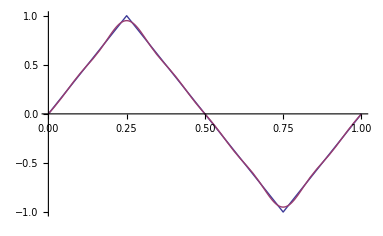

```mathematica
Plot[{TriangleWave[{-1,1},t],TriangleApprox[1,t]},{t,0,1}]
```

```mathematica
b1[t1_]:=NIntegrate[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,0,t1}]
b2[t1_]:=NIntegrate[Gauss[0,0,xcenter1[t],ycenter1[t]]/.vars,{t,0,t1}]
```

```mathematica
Integrate[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,0,.02}]//AbsoluteTiming
Integrate[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,0,.04}]//AbsoluteTiming
Integrate[Gauss[0,0,xcenter1[t],ycenter1[t]]/.vars,{t,0,.02}]//AbsoluteTiming
Integrate[Gauss[0,0,xcenter1[t],ycenter1[t]]/.vars,{t,0,.04}]//AbsoluteTiming
```

{5.6109663,0.00293925}

{13.007212,0.00560894}

{1829.896228,∫_0^0.02 ⅇ^(-5.55556 (-0.810569 Sin[50 π t]+0.0900633 Sin[150 π t]-0.0324228 Sin[250 π t]+0.0165422 Sin[350 π t])^2-5.55556 (-0.810569 Sin[614 π t]+0.0900633 Sin[1842 π t]-0.0324228 Sin[3070 π t]+0.0165422 Sin[4298 π t])^2)ⅆt}

$Aborted

```mathematica
NIntegrate[Gauss[0,0,xcenter1[t],ycenter1[t]]/.vars,{t,0,.08}]//AbsoluteTiming
```

{0.117632,0.0113962}

```mathematica
Parallelize[Plot[{b1[x],b2[x]},{x,0,.06}]]//AbsoluteTiming
```

Parallelize::nopar1: Plot[{b1[x], b2[x]}, {x, 0, 0.06}] cannot be parallelized; proceeding with sequential evaluation.

$Aborted

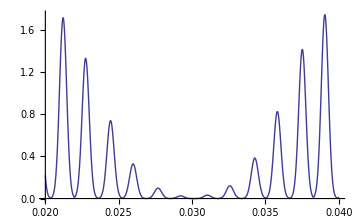

```mathematica
Plot[Gauss[-.05,-.05,xcenter[t],ycenter[t]]/.vars,{t,0.02,.04}]
```

```mathematica
Animate[ContourPlot[Gauss[x,y,xcenter1[t],ycenter1[t]]/.vars,{x,-1,1},{y,-1,1}, PlotRange->{0,1}],{t,0,.01},AnimationRunning->False]
```

```mathematica
f5[t1_]:={t1,1/t1 *Sum[Integrate[Gauss[0,0,xcenter[t],ycenter[t]]/.vars,{t,(i-4)/(2*307),i/(2*307)}],{i,4,t1*2*307,4}]}
points1 = Flatten[Table[{t},{t,2/307,.25,4/(2*307)}],1];
```

```mathematica
?Table
```

Table[expr,{i_max}] generates a list of i_max copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
F[{x_,y_,t_}]:={x,y,Gauss[x,y,xcenter[t],ycenter[t]]/.vars};
points = Flatten[Table[{i,j,n},{i,-1,1,.1},{j,-1,1,.1}],1];
trial=Table[ListContourPlot[ParallelMap[F,points],PlotRange->Full],{n,0,.01,.0001}];
ListAnimate[trial]
```

```mathematica
trial={ParallelMap[F,points/.{n->.0000}],ParallelMap[F,points/.{n->.0001}],ParallelMap[F,points/.{n->.0002}],ParallelMap[F,points/.{n->.0003}],ParallelMap[F,points/.{n->.0004}],ParallelMap[F,points/.{n->.0005}],ParallelMap[F,points/.{n->.0006}],ParallelMap[F,points/.{n->.0007}]};
trial3=ParallelMap[F,points/.{n->.0002}];
trial4=ParallelMap[F,points/.{n->.0003}];
trial5=ParallelMap[F,points/.{n->.0004}];
trial6=ParallelMap[F,points/.{n->.0005}];
trial7=ParallelMap[F,points/.{n->.0006}];
```

```mathematica
P[{x_,y_,z_}]:={2x,2y,2z};
Ppoints= Flatten[Table[{i,j,n},{n,0,.001,.0001},{i,-1,1,.5},{j,-1,1,.5}],{2}]//MatrixForm
Ptrial=Map[F,Ppoints,{2}]//MatrixForm
```

((-1. | -1. | 0.
-1. | -0.5 | 0.
-1. | 0. | 0.
-1. | 0.5 | 0.
-1. | 1. | 0.) | (-1. | -1. | 0.0001
-1. | -0.5 | 0.0001
-1. | 0. | 0.0001
-1. | 0.5 | 0.0001
-1. | 1. | 0.0001) | (-1. | -1. | 0.0002
-1. | -0.5 | 0.0002
-1. | 0. | 0.0002
-1. | 0.5 | 0.0002
-1. | 1. | 0.0002) | (-1. | -1. | 0.0003
-1. | -0.5 | 0.0003
-1. | 0. | 0.0003
-1. | 0.5 | 0.0003
-1. | 1. | 0.0003) | (-1. | -1. | 0.0004
-1. | -0.5 | 0.0004
-1. | 0. | 0.0004
-1. | 0.5 | 0.0004
-1. | 1. | 0.0004) | (-1. | -1. | 0.0005
-1. | -0.5 | 0.0005
-1. | 0. | 0.0005
-1. | 0.5 | 0.0005
-1. | 1. | 0.0005) | (-1. | -1. | 0.0006
-1. | -0.5 | 0.0006
-1. | 0. | 0.0006
-1. | 0.5 | 0.0006
-1. | 1. | 0.0006) | (-1. | -1. | 0.0007
-1. | -0.5 | 0.0007
-1. | 0. | 0.0007
-1. | 0.5 | 0.0007
-1. | 1. | 0.0007) | (-1. | -1. | 0.0008
-1. | -0.5 | 0.0008
-1. | 0. | 0.0008
-1. | 0.5 | 0.0008
-1. | 1. | 0.0008) | (-1. | -1. | 0.0009
-1. | -0.5 | 0.0009
-1. | 0. | 0.0009
-1. | 0.5 | 0.0009
-1. | 1. | 0.0009) | (-1. | -1. | 0.001
-1. | -0.5 | 0.001
-1. | 0. | 0.001
-1. | 0.5 | 0.001
-1. | 1. | 0.001)
(-0.5 | -1. | 0.
-0.5 | -0.5 | 0.
-0.5 | 0. | 0.
-0.5 | 0.5 | 0.
-0.5 | 1. | 0.) | (-0.5 | -1. | 0.0001
-0.5 | -0.5 | 0.0001
-0.5 | 0. | 0.0001
-0.5 | 0.5 | 0.0001
-0.5 | 1. | 0.0001) | (-0.5 | -1. | 0.0002
-0.5 | -0.5 | 0.0002
-0.5 | 0. | 0.0002
-0.5 | 0.5 | 0.0002
-0.5 | 1. | 0.0002) | (-0.5 | -1. | 0.0003
-0.5 | -0.5 | 0.0003
-0.5 | 0. | 0.0003
-0.5 | 0.5 | 0.0003
-0.5 | 1. | 0.0003) | (-0.5 | -1. | 0.0004
-0.5 | -0.5 | 0.0004
-0.5 | 0. | 0.0004
-0.5 | 0.5 | 0.0004
-0.5 | 1. | 0.0004) | (-0.5 | -1. | 0.0005
-0.5 | -0.5 | 0.0005
-0.5 | 0. | 0.0005
-0.5 | 0.5 | 0.0005
-0.5 | 1. | 0.0005) | (-0.5 | -1. | 0.0006
-0.5 | -0.5 | 0.0006
-0.5 | 0. | 0.0006
-0.5 | 0.5 | 0.0006
-0.5 | 1. | 0.0006) | (-0.5 | -1. | 0.0007
-0.5 | -0.5 | 0.0007
-0.5 | 0. | 0.0007
-0.5 | 0.5 | 0.0007
-0.5 | 1. | 0.0007) | (-0.5 | -1. | 0.0008
-0.5 | -0.5 | 0.0008
-0.5 | 0. | 0.0008
-0.5 | 0.5 | 0.0008
-0.5 | 1. | 0.0008) | (-0.5 | -1. | 0.0009
-0.5 | -0.5 | 0.0009
-0.5 | 0. | 0.0009
-0.5 | 0.5 | 0.0009
-0.5 | 1. | 0.0009) | (-0.5 | -1. | 0.001
-0.5 | -0.5 | 0.001
-0.5 | 0. | 0.001
-0.5 | 0.5 | 0.001
-0.5 | 1. | 0.001)
(0. | -1. | 0.
0. | -0.5 | 0.
0. | 0. | 0.
0. | 0.5 | 0.
0. | 1. | 0.) | (0. | -1. | 0.0001
0. | -0.5 | 0.0001
0. | 0. | 0.0001
0. | 0.5 | 0.0001
0. | 1. | 0.0001) | (0. | -1. | 0.0002
0. | -0.5 | 0.0002
0. | 0. | 0.0002
0. | 0.5 | 0.0002
0. | 1. | 0.0002) | (0. | -1. | 0.0003
0. | -0.5 | 0.0003
0. | 0. | 0.0003
0. | 0.5 | 0.0003
0. | 1. | 0.0003) | (0. | -1. | 0.0004
0. | -0.5 | 0.0004
0. | 0. | 0.0004
0. | 0.5 | 0.0004
0. | 1. | 0.0004) | (0. | -1. | 0.0005
0. | -0.5 | 0.0005
0. | 0. | 0.0005
0. | 0.5 | 0.0005
0. | 1. | 0.0005) | (0. | -1. | 0.0006
0. | -0.5 | 0.0006
0. | 0. | 0.0006
0. | 0.5 | 0.0006
0. | 1. | 0.0006) | (0. | -1. | 0.0007
0. | -0.5 | 0.0007
0. | 0. | 0.0007
0. | 0.5 | 0.0007
0. | 1. | 0.0007) | (0. | -1. | 0.0008
0. | -0.5 | 0.0008
0. | 0. | 0.0008
0. | 0.5 | 0.0008
0. | 1. | 0.0008) | (0. | -1. | 0.0009
0. | -0.5 | 0.0009
0. | 0. | 0.0009
0. | 0.5 | 0.0009
0. | 1. | 0.0009) | (0. | -1. | 0.001
0. | -0.5 | 0.001
0. | 0. | 0.001
0. | 0.5 | 0.001
0. | 1. | 0.001)
(0.5 | -1. | 0.
0.5 | -0.5 | 0.
0.5 | 0. | 0.
0.5 | 0.5 | 0.
0.5 | 1. | 0.) | (0.5 | -1. | 0.0001
0.5 | -0.5 | 0.0001
0.5 | 0. | 0.0001
0.5 | 0.5 | 0.0001
0.5 | 1. | 0.0001) | (0.5 | -1. | 0.0002
0.5 | -0.5 | 0.0002
0.5 | 0. | 0.0002
0.5 | 0.5 | 0.0002
0.5 | 1. | 0.0002) | (0.5 | -1. | 0.0003
0.5 | -0.5 | 0.0003
0.5 | 0. | 0.0003
0.5 | 0.5 | 0.0003
0.5 | 1. | 0.0003) | (0.5 | -1. | 0.0004
0.5 | -0.5 | 0.0004
0.5 | 0. | 0.0004
0.5 | 0.5 | 0.0004
0.5 | 1. | 0.0004) | (0.5 | -1. | 0.0005
0.5 | -0.5 | 0.0005
0.5 | 0. | 0.0005
0.5 | 0.5 | 0.0005
0.5 | 1. | 0.0005) | (0.5 | -1. | 0.0006
0.5 | -0.5 | 0.0006
0.5 | 0. | 0.0006
0.5 | 0.5 | 0.0006
0.5 | 1. | 0.0006) | (0.5 | -1. | 0.0007
0.5 | -0.5 | 0.0007
0.5 | 0. | 0.0007
0.5 | 0.5 | 0.0007
0.5 | 1. | 0.0007) | (0.5 | -1. | 0.0008
0.5 | -0.5 | 0.0008
0.5 | 0. | 0.0008
0.5 | 0.5 | 0.0008
0.5 | 1. | 0.0008) | (0.5 | -1. | 0.0009
0.5 | -0.5 | 0.0009
0.5 | 0. | 0.0009
0.5 | 0.5 | 0.0009
0.5 | 1. | 0.0009) | (0.5 | -1. | 0.001
0.5 | -0.5 | 0.001
0.5 | 0. | 0.001
0.5 | 0.5 | 0.001
0.5 | 1. | 0.001)
(1. | -1. | 0.
1. | -0.5 | 0.
1. | 0. | 0.
1. | 0.5 | 0.
1. | 1. | 0.) | (1. | -1. | 0.0001
1. | -0.5 | 0.0001
1. | 0. | 0.0001
1. | 0.5 | 0.0001
1. | 1. | 0.0001) | (1. | -1. | 0.0002
1. | -0.5 | 0.0002
1. | 0. | 0.0002
1. | 0.5 | 0.0002
1. | 1. | 0.0002) | (1. | -1. | 0.0003
1. | -0.5 | 0.0003
1. | 0. | 0.0003
1. | 0.5 | 0.0003
1. | 1. | 0.0003) | (1. | -1. | 0.0004
1. | -0.5 | 0.0004
1. | 0. | 0.0004
1. | 0.5 | 0.0004
1. | 1. | 0.0004) | (1. | -1. | 0.0005
1. | -0.5 | 0.0005
1. | 0. | 0.0005
1. | 0.5 | 0.0005
1. | 1. | 0.0005) | (1. | -1. | 0.0006
1. | -0.5 | 0.0006
1. | 0. | 0.0006
1. | 0.5 | 0.0006
1. | 1. | 0.0006) | (1. | -1. | 0.0007
1. | -0.5 | 0.0007
1. | 0. | 0.0007
1. | 0.5 | 0.0007
1. | 1. | 0.0007) | (1. | -1. | 0.0008
1. | -0.5 | 0.0008
1. | 0. | 0.0008
1. | 0.5 | 0.0008
1. | 1. | 0.0008) | (1. | -1. | 0.0009
1. | -0.5 | 0.0009
1. | 0. | 0.0009
1. | 0.5 | 0.0009
1. | 1. | 0.0009) | (1. | -1. | 0.001
1. | -0.5 | 0.001
1. | 0. | 0.001
1. | 0.5 | 0.001
1. | 1. | 0.001))

(F[{{{-1.,-1.,0.},{-1.,-0.5,0.},{-1.,0.,0.},{-1.,0.5,0.},{-1.,1.,0.}},{{-1.,-1.,0.0001},{-1.,-0.5,0.0001},{-1.,0.,0.0001},{-1.,0.5,0.0001},{-1.,1.,0.0001}},{{-1.,-1.,0.0002},{-1.,-0.5,0.0002},{-1.,0.,0.0002},{-1.,0.5,0.0002},{-1.,1.,0.0002}},{{-1.,-1.,0.0003},{-1.,-0.5,0.0003},{-1.,0.,0.0003},{-1.,0.5,0.0003},{-1.,1.,0.0003}},{{-1.,-1.,0.0004},{-1.,-0.5,0.0004},{-1.,0.,0.0004},{-1.,0.5,0.0004},{-1.,1.,0.0004}},{{-1.,-1.,0.0005},{-1.,-0.5,0.0005},{-1.,0.,0.0005},{-1.,0.5,0.0005},{-1.,1.,0.0005}},{{-1.,-1.,0.0006},{-1.,-0.5,0.0006},{-1.,0.,0.0006},{-1.,0.5,0.0006},{-1.,1.,0.0006}},{{-1.,-1.,0.0007},{-1.,-0.5,0.0007},{-1.,0.,0.0007},{-1.,0.5,0.0007},{-1.,1.,0.0007}},{{-1.,-1.,0.0008},{-1.,-0.5,0.0008},{-1.,0.,0.0008},{-1.,0.5,0.0008},{-1.,1.,0.0008}},{{-1.,-1.,0.0009},{-1.,-0.5,0.0009},{-1.,0.,0.0009},{-1.,0.5,0.0009},{-1.,1.,0.0009}},{{-1.,-1.,0.001},{-1.,-0.5,0.001},{-1.,0.,0.001},{-1.,0.5,0.001},{-1.,1.,0.001}}}]
F[{{{-0.5,-1.,0.},{-0.5,-0.5,0.},{-0.5,0.,0.},{-0.5,0.5,0.},{-0.5,1.,0.}},{{-0.5,-1.,0.0001},{-0.5,-0.5,0.0001},{-0.5,0.,0.0001},{-0.5,0.5,0.0001},{-0.5,1.,0.0001}},{{-0.5,-1.,0.0002},{-0.5,-0.5,0.0002},{-0.5,0.,0.0002},{-0.5,0.5,0.0002},{-0.5,1.,0.0002}},{{-0.5,-1.,0.0003},{-0.5,-0.5,0.0003},{-0.5,0.,0.0003},{-0.5,0.5,0.0003},{-0.5,1.,0.0003}},{{-0.5,-1.,0.0004},{-0.5,-0.5,0.0004},{-0.5,0.,0.0004},{-0.5,0.5,0.0004},{-0.5,1.,0.0004}},{{-0.5,-1.,0.0005},{-0.5,-0.5,0.0005},{-0.5,0.,0.0005},{-0.5,0.5,0.0005},{-0.5,1.,0.0005}},{{-0.5,-1.,0.0006},{-0.5,-0.5,0.0006},{-0.5,0.,0.0006},{-0.5,0.5,0.0006},{-0.5,1.,0.0006}},{{-0.5,-1.,0.0007},{-0.5,-0.5,0.0007},{-0.5,0.,0.0007},{-0.5,0.5,0.0007},{-0.5,1.,0.0007}},{{-0.5,-1.,0.0008},{-0.5,-0.5,0.0008},{-0.5,0.,0.0008},{-0.5,0.5,0.0008},{-0.5,1.,0.0008}},{{-0.5,-1.,0.0009},{-0.5,-0.5,0.0009},{-0.5,0.,0.0009},{-0.5,0.5,0.0009},{-0.5,1.,0.0009}},{{-0.5,-1.,0.001},{-0.5,-0.5,0.001},{-0.5,0.,0.001},{-0.5,0.5,0.001},{-0.5,1.,0.001}}}]
F[{{{0.,-1.,0.},{0.,-0.5,0.},{0.,0.,0.},{0.,0.5,0.},{0.,1.,0.}},{{0.,-1.,0.0001},{0.,-0.5,0.0001},{0.,0.,0.0001},{0.,0.5,0.0001},{0.,1.,0.0001}},{{0.,-1.,0.0002},{0.,-0.5,0.0002},{0.,0.,0.0002},{0.,0.5,0.0002},{0.,1.,0.0002}},{{0.,-1.,0.0003},{0.,-0.5,0.0003},{0.,0.,0.0003},{0.,0.5,0.0003},{0.,1.,0.0003}},{{0.,-1.,0.0004},{0.,-0.5,0.0004},{0.,0.,0.0004},{0.,0.5,0.0004},{0.,1.,0.0004}},{{0.,-1.,0.0005},{0.,-0.5,0.0005},{0.,0.,0.0005},{0.,0.5,0.0005},{0.,1.,0.0005}},{{0.,-1.,0.0006},{0.,-0.5,0.0006},{0.,0.,0.0006},{0.,0.5,0.0006},{0.,1.,0.0006}},{{0.,-1.,0.0007},{0.,-0.5,0.0007},{0.,0.,0.0007},{0.,0.5,0.0007},{0.,1.,0.0007}},{{0.,-1.,0.0008},{0.,-0.5,0.0008},{0.,0.,0.0008},{0.,0.5,0.0008},{0.,1.,0.0008}},{{0.,-1.,0.0009},{0.,-0.5,0.0009},{0.,0.,0.0009},{0.,0.5,0.0009},{0.,1.,0.0009}},{{0.,-1.,0.001},{0.,-0.5,0.001},{0.,0.,0.001},{0.,0.5,0.001},{0.,1.,0.001}}}]
F[{{{0.5,-1.,0.},{0.5,-0.5,0.},{0.5,0.,0.},{0.5,0.5,0.},{0.5,1.,0.}},{{0.5,-1.,0.0001},{0.5,-0.5,0.0001},{0.5,0.,0.0001},{0.5,0.5,0.0001},{0.5,1.,0.0001}},{{0.5,-1.,0.0002},{0.5,-0.5,0.0002},{0.5,0.,0.0002},{0.5,0.5,0.0002},{0.5,1.,0.0002}},{{0.5,-1.,0.0003},{0.5,-0.5,0.0003},{0.5,0.,0.0003},{0.5,0.5,0.0003},{0.5,1.,0.0003}},{{0.5,-1.,0.0004},{0.5,-0.5,0.0004},{0.5,0.,0.0004},{0.5,0.5,0.0004},{0.5,1.,0.0004}},{{0.5,-1.,0.0005},{0.5,-0.5,0.0005},{0.5,0.,0.0005},{0.5,0.5,0.0005},{0.5,1.,0.0005}},{{0.5,-1.,0.0006},{0.5,-0.5,0.0006},{0.5,0.,0.0006},{0.5,0.5,0.0006},{0.5,1.,0.0006}},{{0.5,-1.,0.0007},{0.5,-0.5,0.0007},{0.5,0.,0.0007},{0.5,0.5,0.0007},{0.5,1.,0.0007}},{{0.5,-1.,0.0008},{0.5,-0.5,0.0008},{0.5,0.,0.0008},{0.5,0.5,0.0008},{0.5,1.,0.0008}},{{0.5,-1.,0.0009},{0.5,-0.5,0.0009},{0.5,0.,0.0009},{0.5,0.5,0.0009},{0.5,1.,0.0009}},{{0.5,-1.,0.001},{0.5,-0.5,0.001},{0.5,0.,0.001},{0.5,0.5,0.001},{0.5,1.,0.001}}}]
F[{{{1.,-1.,0.},{1.,-0.5,0.},{1.,0.,0.},{1.,0.5,0.},{1.,1.,0.}},{{1.,-1.,0.0001},{1.,-0.5,0.0001},{1.,0.,0.0001},{1.,0.5,0.0001},{1.,1.,0.0001}},{{1.,-1.,0.0002},{1.,-0.5,0.0002},{1.,0.,0.0002},{1.,0.5,0.0002},{1.,1.,0.0002}},{{1.,-1.,0.0003},{1.,-0.5,0.0003},{1.,0.,0.0003},{1.,0.5,0.0003},{1.,1.,0.0003}},{{1.,-1.,0.0004},{1.,-0.5,0.0004},{1.,0.,0.0004},{1.,0.5,0.0004},{1.,1.,0.0004}},{{1.,-1.,0.0005},{1.,-0.5,0.0005},{1.,0.,0.0005},{1.,0.5,0.0005},{1.,1.,0.0005}},{{1.,-1.,0.0006},{1.,-0.5,0.0006},{1.,0.,0.0006},{1.,0.5,0.0006},{1.,1.,0.0006}},{{1.,-1.,0.0007},{1.,-0.5,0.0007},{1.,0.,0.0007},{1.,0.5,0.0007},{1.,1.,0.0007}},{{1.,-1.,0.0008},{1.,-0.5,0.0008},{1.,0.,0.0008},{1.,0.5,0.0008},{1.,1.,0.0008}},{{1.,-1.,0.0009},{1.,-0.5,0.0009},{1.,0.,0.0009},{1.,0.5,0.0009},{1.,1.,0.0009}},{{1.,-1.,0.001},{1.,-0.5,0.001},{1.,0.,0.001},{1.,0.5,0.001},{1.,1.,0.001}}}])

```mathematica
ListAnimate[Table[ListContourPlot[Ptrial[[n]],PlotRange->Full],{n,1,8}]]
```

```mathematica
f6[x_,y_,t1_]:={t1,1/t1 *Sum[Integrate[Gauss[x,y,xcenter[t],ycenter[t]]/.vars,{t,(i-4)/(2*307),i/(2*307)}],{i,4,t1*2*307,4}]}
points1 = Flatten[Table[{t},{t,2/307,.25,4/(2*307)}],1];
```